```mathematica
PartitionTypeLattice2[form_]:=Block[e
Table[
If[IsTypeRefinement[pair[[1]],pair[[2]]],
AppendTo[result,DirectedEdge[pair[[1]],pair[[2]]]],
If[IsTypeRefinement[pair[[2]],pair[[1]]],
AppendTo[result,DirectedEdge[pair[[2]],pair[[1]]]]
]
]
,
{pair,com}
];
Graph[
result,GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[SymbolToSets[#]->Rotate[Column[{#,Style[Coefficient[form,#],Bold,Red]}, Alignment->Center],Pi/4]&,vars]
]
]
```

```mathematica
PartitionTypeFormula[allGraphs5[0,"graph"]]
```

p1x1x1x1x1+10 p2x1x1x1+15 p2x2x1+10 p3x1x1+10 p3x2+5 p4x1+p5

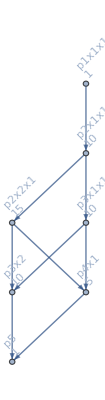

```mathematica
PartitionTypeLattice2[PartitionTypeFormula[allGraphs5[0,"graph"]]]
```

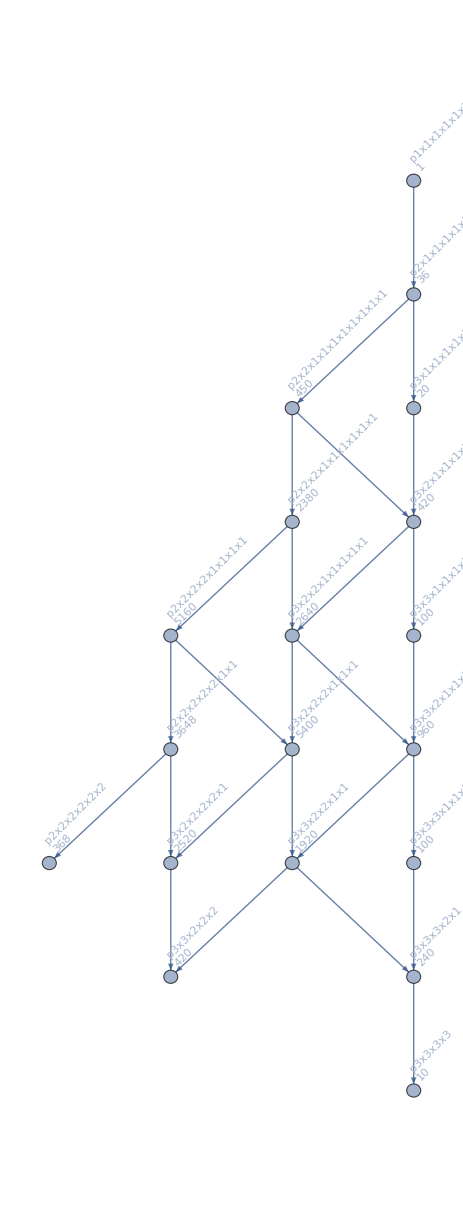

```mathematica
PartitionTypeLattice2[PartitionTypeFormula[Graph[plantri[[1]]]]]
```

```mathematica
FindEmptyFormula[CompleteGraph[4]]//Total
```

-6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4

```mathematica
allGraphs4[K4Key,"colofourrealnull"]
```

-6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4

```mathematica
NullPartitionTypeFormula[g_Graph]:=Total[Map[With[{var=First[ListofVars[#]]},
With[{p=SetsToPartitionTypeSymbol[SymbolToSets[var]]},
Coefficient[#,var]*p]]&,FindEmptyFormula[g]]]
```

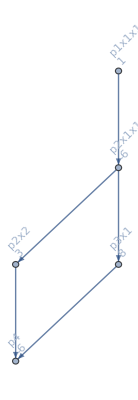

```mathematica
NullPartitionTypeFormula[CompleteGraph[4]]//PartitionTypeLattice2
```

```mathematica
PartitionTypeFormula[CompleteGraph[4]]
```

p1x1x1x1

```mathematica
Map[With[{var=First[ListofVars[#]]},
With[{p=SetsToPartitionTypeSymbol[SymbolToSets[var]]},
Coefficient[#,var]*p]]&,{n1x2x3x4,-n1x2x34,-n1x24x3,n1x234,-n1x23x4,n1x234,-n14x2x3,n134x2,n124x3,-n1234,n14x23,-n1234,-n13x2x4,n134x2,n123x4,-n1234,n13x24,-n1234,-n12x3x4,n124x3,n123x4,-n1234,n12x34,-n1234}]
```

{p1x1x1x1,-p2x1x1,-p2x1x1,p3x1,-p2x1x1,p3x1,-p2x1x1,p3x1,p3x1,-p4,p2x2,-p4,-p2x1x1,p3x1,p3x1,-p4,p2x2,-p4,-p2x1x1,p3x1,p3x1,-p4,p2x2,-p4}

```mathematica
Graph[PartitionTypeLattice[IntegerPartitions[5]],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->"Name"]
```

-Graphics-

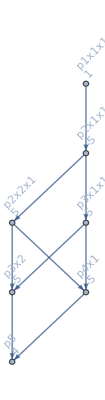
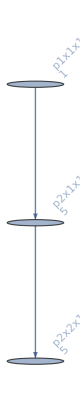
{-Graphics-p1x1x1x1x1-5 p2x1x1x1+5 p2x2x1+5 p3x1x1-5 p3x2-5 p4x1+4 p5,-Graphics-p1x1x1x1x1+5 p2x1x1x1+5 p2x2x1}

```mathematica
Table[With[{form=op[allGraphs5[lambdaKey,"graph"]]},Labeled[form//PartitionTypeLattice2,form]],{op,{NullPartitionTypeFormula,PartitionTypeFormula}}]
```

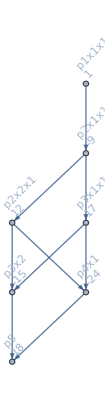
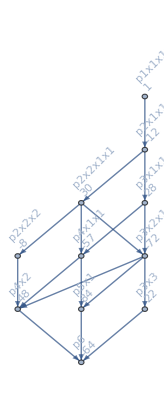
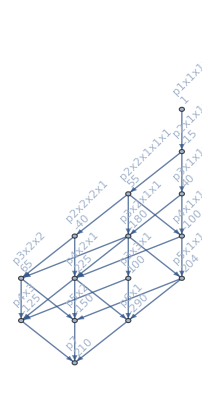
{-Graphics-p1x1x1x1x1-9 p2x1x1x1+12 p2x2x1+17 p3x1x1-15 p3x2-24 p4x1+18 p5,-Graphics-p1x1x1x1x1x1-12 p2x1x1x1x1+30 p2x2x1x1-8 p2x2x2+28 p3x1x1x1-72 p3x2x1+22 p3x3-57 p4x1x1+48 p4x2+84 p5x1-64 p6,-Graphics-p1x1x1x1x1x1x1-15 p2x1x1x1x1x1+55 p2x2x1x1x1-40 p2x2x2x1+40 p3x1x1x1x1-180 p3x2x1x1+65 p3x2x2+100 p3x3x1-100 p4x1x1x1+225 p4x2x1-125 p4x3+204 p5x1x1-150 p5x2-290 p6x1+210 p7}

```mathematica
Table[With[{form=NullPartitionTypeFormula[JacobsThalGraph[k]]},Labeled[form//PartitionTypeLattice2,form]],{k,3}]
```

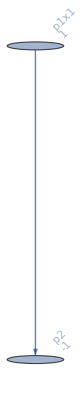
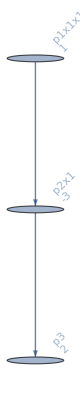
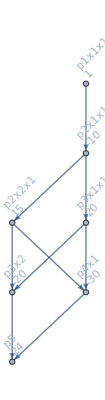
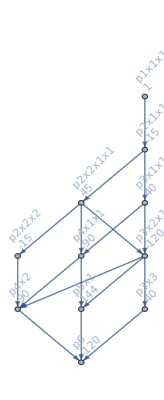
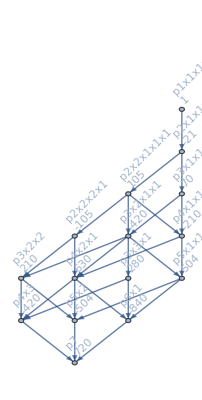
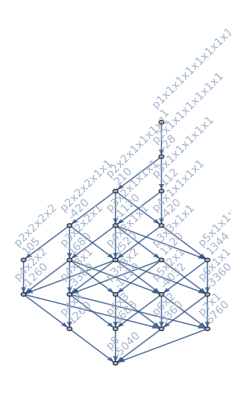
{-Graphics-p1,-Graphics-p1x1-p2,-Graphics-p1x1x1-3 p2x1+2 p3,-Graphics-p1x1x1x1-6 p2x1x1+3 p2x2+8 p3x1-6 p4,-Graphics-p1x1x1x1x1-10 p2x1x1x1+15 p2x2x1+20 p3x1x1-20 p3x2-30 p4x1+24 p5,-Graphics-p1x1x1x1x1x1-15 p2x1x1x1x1+45 p2x2x1x1-15 p2x2x2+40 p3x1x1x1-120 p3x2x1+40 p3x3-90 p4x1x1+90 p4x2+144 p5x1-120 p6,-Graphics-p1x1x1x1x1x1x1-21 p2x1x1x1x1x1+105 p2x2x1x1x1-105 p2x2x2x1+70 p3x1x1x1x1-420 p3x2x1x1+210 p3x2x2+280 p3x3x1-210 p4x1x1x1+630 p4x2x1-420 p4x3+504 p5x1x1-504 p5x2-840 p6x1+720 p7,-Graphics-p1x1x1x1x1x1x1x1-28 p2x1x1x1x1x1x1+210 p2x2x1x1x1x1-420 p2x2x2x1x1+105 p2x2x2x2+112 p3x1x1x1x1x1-1120 p3x2x1x1x1+1680 p3x2x2x1+1120 p3x3x1x1-1120 p3x3x2-420 p4x1x1x1x1+2520 p4x2x1x1-1260 p4x2x2-3360 p4x3x1+1260 p4x4+1344 p5x1x1x1-4032 p5x2x1+2688 p5x3-3360 p6x1x1+3360 p6x2+5760 p7x1-5040 p8}

```mathematica
Table[With[{form=NullPartitionTypeFormula[CompleteGraph[k]]},Labeled[form//PartitionTypeLattice2,form]],{k,8}]
```

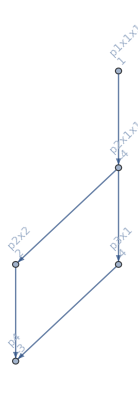
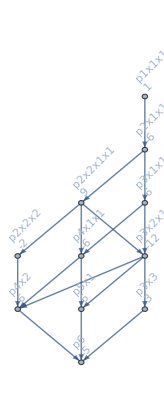
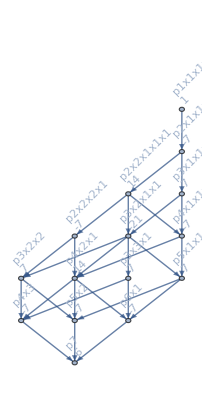
{-Graphics-p1x1x1-3 p2x1+2 p3,-Graphics-p1x1x1x1-4 p2x1x1+2 p2x2+4 p3x1-3 p4,-Graphics-p1x1x1x1x1-5 p2x1x1x1+5 p2x2x1+5 p3x1x1-5 p3x2-5 p4x1+4 p5,-Graphics-p1x1x1x1x1x1-6 p2x1x1x1x1+9 p2x2x1x1-2 p2x2x2+6 p3x1x1x1-12 p3x2x1+3 p3x3-6 p4x1x1+6 p4x2+6 p5x1-5 p6,-Graphics-p1x1x1x1x1x1x1-7 p2x1x1x1x1x1+14 p2x2x1x1x1-7 p2x2x2x1+7 p3x1x1x1x1-21 p3x2x1x1+7 p3x2x2+7 p3x3x1-7 p4x1x1x1+14 p4x2x1-7 p4x3+7 p5x1x1-7 p5x2-7 p6x1+6 p7}

```mathematica
Table[With[{form=NullPartitionTypeFormula[CycleGraph[k]]},Labeled[form//PartitionTypeLattice2,form]],{k,3,7}]
```

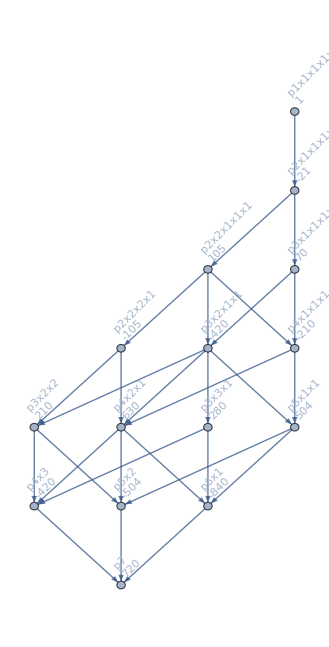
```mathematica
PropertyValue[-Graphics-,VertexLabels]
```

{{{3},{1},{1},{1},{1}}→p3x1x1x1x1
70,{{1},{1},{1},{1},{1},{1},{1}}→p1x1x1x1x1x1x1
1,{{2},{2},{2},{1}}→p2x2x2x1
-105,{{4},{1},{1},{1}}→p4x1x1x1
-210,{{4},{2},{1}}→p4x2x1
630,{{2},{2},{1},{1},{1}}→p2x2x1x1x1
105,{{2},{1},{1},{1},{1},{1}}→p2x1x1x1x1x1
-21,{{5},{1},{1}}→p5x1x1
504,{{3},{2},{1},{1}}→p3x2x1x1
-420,{{7}}→p7
720,{{3},{2},{2}}→p3x2x2
210,{{5},{2}}→p5x2
-504,{{4},{3}}→p4x3
-420,{{6},{1}}→p6x1
-840,{{3},{3},{1}}→p3x3x1
280}

```mathematica
PartitionTypeLattice[IntegerPartitions[4]]
```

{{3,1}->{4},{2,2}->{4},{2,1,1}->{3,1},{2,1,1}->{2,2},{1,1,1,1}->{2,1,1}}

```mathematica
Table[With[{form=PartitionTypeFormula[CycleGraph[k]]},Labeled[Graph[PartitionTypeLattice[IntegerPartitions[k]],GraphHighlight->EdgeList[form//PartitionTypeLattice2]],form]],{k,4,6}]
```

{Graph[{{3,1}->{4},{2,2}->{4},{2,1,1}->{3,1},{2,1,1}->{2,2},{1,1,1,1}->{2,1,1}},GraphHighlight->{{{1},{1},{1},{1}}->{{2},{1},{1}},{{2},{1},{1}}->{{2},{2}}}]p1x1x1x1+2 p2x1x1+p2x2,Graph[{{4,1}->{5},{3,2}->{5},{3,1,1}->{4,1},{2,2,1}->{4,1},{3,1,1}->{3,2},{2,2,1}->{3,2},{2,1,1,1}->{3,1,1},{2,1,1,1}->{2,2,1},{1,1,1,1,1}->{2,1,1,1}},GraphHighlight->{{{1},{1},{1},{1},{1}}->{{2},{1},{1},{1}},{{2},{1},{1},{1}}->{{2},{2},{1}}}]p1x1x1x1x1+5 p2x1x1x1+5 p2x2x1,Graph[{{5,1}->{6},{4,2}->{6},{3,3}->{6},{4,1,1}->{5,1},{3,2,1}->{5,1},{4,1,1}->{4,2},{3,2,1}->{4,2},{2,2,2}->{4,2},{3,1,1,1}->{4,1,1},{2,2,1,1}->{4,1,1},{3,2,1}->{3,3},{3,1,1,1}->{3,2,1},{2,2,1,1}->{3,2,1},{2,1,1,1,1}->{3,1,1,1},{2,2,1,1}->{2,2,2},{2,1,1,1,1}->{2,2,1,1},{1,1,1,1,1,1}->{2,1,1,1,1}},GraphHighlight->{{{1},{1},{1},{1},{1},{1}}->{{2},{1},{1},{1},{1}},{{3},{2},{1}}->{{3},{3}},{{2},{1},{1},{1},{1}}->{{2},{2},{1},{1}},{{2},{1},{1},{1},{1}}->{{3},{1},{1},{1}},{{2},{2},{1},{1}}->{{2},{2},{2}},{{2},{2},{1},{1}}->{{3},{2},{1}},{{3},{1},{1},{1}}->{{3},{2},{1}}}]p1x1x1x1x1x1+9 p2x1x1x1x1+18 p2x2x1x1+4 p2x2x2+2 p3x1x1x1+6 p3x2x1+p3x3}

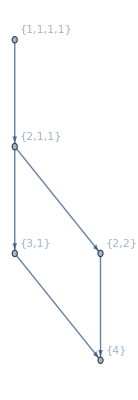
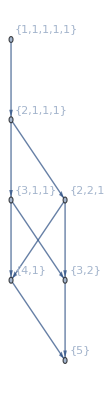
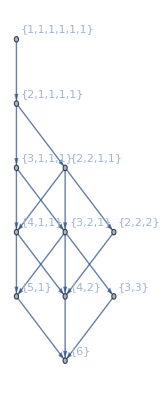
{-Graphics-p1x1x1x1+2 p2x1x1+p2x2,-Graphics-p1x1x1x1x1+5 p2x1x1x1+5 p2x2x1,-Graphics-p1x1x1x1x1x1+9 p2x1x1x1x1+18 p2x2x1x1+4 p2x2x2+2 p3x1x1x1+6 p3x2x1+p3x3}

```mathematica
Table[With[{form=PartitionTypeFormula[CycleGraph[k]]},Labeled[Graph[PartitionTypeLattice[IntegerPartitions[k]], VertexLabels->"Name"],form]],{k,4,6}]
```